```mathematica
QHeatFlow=Abs[3/(4 ξ^3)-1/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))];
(*{d->1.1};*)
QHeatFlowg=Manipulate[LogLogPlot[Abs[3/(4 ξ^3)-1/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))],{ξ,0.001,100000},PlotLabel->Q^-1/ΔE, Frame->True,FrameLabel->{ξ,Q^-1/ΔE}],{d,1,2,0.1}]
```

壁になっているところ拡大

```mathematica
QHeatFlow=Abs[3/(4 ξ^3)-1/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))];
(*{d->1.1};*)
QHeatFlowg=Manipulate[LogLogPlot[Abs[3/(4 ξ^3)1/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))],{ξ,340,370},PlotLabel->Q^-1/ΔE, Frame->True,FrameLabel->{ξ,Q^-1/ΔE}],{d,1,2,0.1}]
```

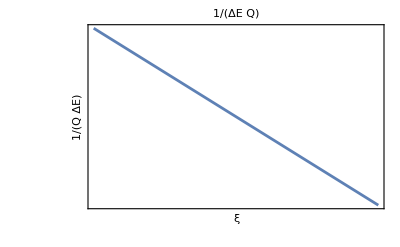

```mathematica
QNoHeatFlow = Abs[6/(2ξ)^2-6/(2ξ)^3(Sinh[2ξ]+Sin[2ξ])/(Cosh[2ξ]+Cos[2ξ])] ;


QNoHeatFlowg=LogLogPlot[QNoHeatFlow,{ξ,340,370},PlotLabel->Q^-1/ΔE, Frame->True,FrameLabel->{ξ,Q^-1/ΔE}]
```

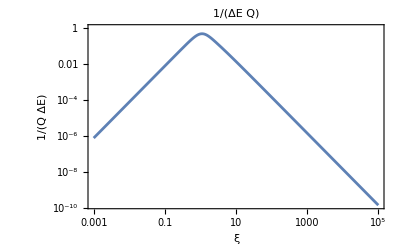

```mathematica
QNoHeatFlow = Abs[6/(2ξ)^2-6/(2ξ)^3(Sinh[2ξ]+Sin[2ξ])/(Cosh[2ξ]+Cos[2ξ])] ;


QNoHeatFlowg=LogLogPlot[QNoHeatFlow,{ξ,0.001,100000},PlotLabel->Q^-1/ΔE, Frame->True,FrameLabel->{ξ,Q^-1/ΔE}]
```

熱流ありのとなしのを並べる

```mathematica
Manipulate[LogLogPlot[{Abs[3/(4 ξ^3)-1/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))],QNoHeatFlow},(*PlotStyle->{RightBlue,Dashed},*){ξ,0.001,100000},PlotLabel->Q^-1/ΔE, Frame->True,FrameLabel->{ξ,Q^-1/ΔE}],{d,1,2,0.1}]
```

```mathematica
Manipulate[LogLinearPlot[{3/(4 ξ^3)-1/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)])),QNoHeatFlow},(*PlotStyle->{RightBlue,Dashed},*){ξ,0.001,1000},PlotLabel->Q^-1/ΔE, Frame->True,FrameLabel->{ξ,Q^-1/ΔE}],{d,1,2,0.1}]
```